```mathematica
ϕ[x_,y_]:=Piecewise[{{1-x-y+x*y, 1≥x≥0&&1≥ y≥0}, {1+x-y-x*y, -1≤x≤0&&1≥y≥0}, {1+x+y+x*y, -1≤x≤0&&-1≤y≤0}, {1-x+y-x*y, 1≥x≥0&&-1≤y≤0}, {0, True}}]
xi = .2; yi = .4;
h = .1;
Plot3D[ϕ[(x-xi)/h,(y-yi)/h],{x,-2,2},{y,-2,2},PlotRange->All,PlotPoints->150]
```

-Graphics3D-

```mathematica
ϕ[(x-xi)/h,(y-yi)/h]
```

Piecewise[{{1-10. (-0.2+x)-10. (-0.4+y)+100. (-0.2+x) (-0.4+y), 1≥10. (-0.2+x)≥0&&1≥10. (-0.4+y)≥0}, {1+10. (-0.2+x)-10. (-0.4+y)-100. (-0.2+x) (-0.4+y), -1≤10. (-0.2+x)≤0&&1≥10. (-0.4+y)≥0}, {1+10. (-0.2+x)+10. (-0.4+y)+100. (-0.2+x) (-0.4+y), -1≤10. (-0.2+x)≤0&&-1≤10. (-0.4+y)≤0}, {1-10. (-0.2+x)+10. (-0.4+y)-100. (-0.2+x) (-0.4+y), 1≥10. (-0.2+x)≥0&&-1≤10. (-0.4+y)≤0}, {0, True}}]

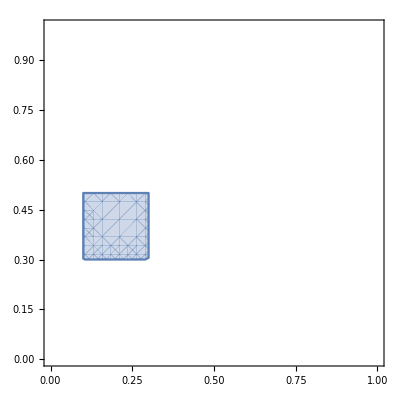

-Graphics3D-

```mathematica
RegionPlot[1≥10. (-0.2+x)≥0&&1≥10. (-0.4+y)≥0||-1≤10. (-0.2+x)≤0&&1≥10. (-0.4+y)≥0||-1≤10. (-0.2+x)≤0&&-1≤10. (-0.4+y)≤0||1≥10. (-0.2+x)≥0&&-1≤10. (-0.4+y)≤0,{x,0,1},{y,0,1}]
```

```mathematica
a=-1;
b=1;
xi=0;
yi = 0;
h = 0.5;
Plot3D[ϕ[(x-xi)*h,(y-yi)*h],{x,a,b},{y,a,b},PlotRange->All]
```

-Graphics3D-

```mathematica
ϕ[0,0]
```

1

```mathematica
ϕ[(x-xi)/h,(y-yi)/h]
```

Piecewise[{{1-2. (-2+x)-2. (-1+y)+4. (-2+x) (-1+y), 1≥2. (-2+x)≥0&&1≥2. (-1+y)≥0}, {1+2. (-2+x)-2. (-1+y)-4. (-2+x) (-1+y), -1≤2. (-2+x)≤0&&1≥2. (-1+y)≥0}, {1+2. (-2+x)+2. (-1+y)+4. (-2+x) (-1+y), -1≤2. (-2+x)≤0&&-1≤2. (-1+y)≤0}, {1-2. (-2+x)+2. (-1+y)-4. (-2+x) (-1+y), 1≥2. (-2+x)≥0&&-1≤2. (-1+y)≤0}, {0, True}}]

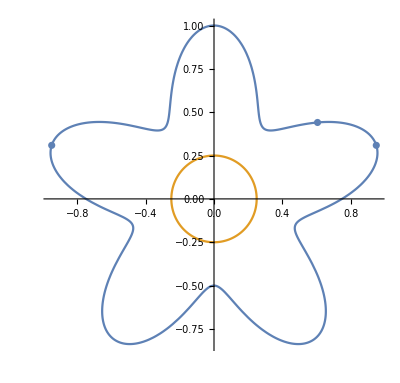

```mathematica
fo[r_,θ_]:=r - 0.75-0.25*Sin[5θ];
Show[PolarPlot[{0.75+0.25*Sin[5θ],.25},{θ,0,2 π}],ListPlot[{{Cos[π/10],Sin[π/10]},{0.75Cos[2π/10],0.75Sin[2π/10]},{Cos[9π/10],Sin[9π/10]}}]]
```

```mathematica
5*θ == π/2
```

```mathematica
??PolarPlot
```

PolarPlot[r,{θ,θ_min,θ_max}] generates a polar plot of a curve with radius r as a function of angle θ.
PolarPlot[{f_1,f_2,…},{θ,θ_min,θ_max}] makes a polar plot of curves with radius functions f_1, f_2, ….

Attributes[PolarPlot]={Protected,ReadProtected}

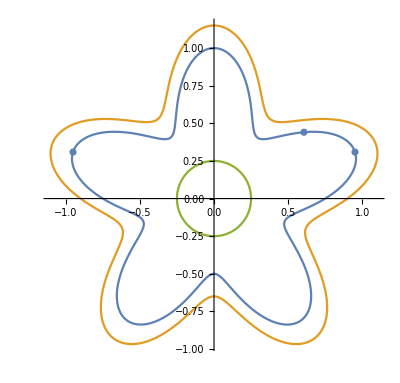

```mathematica
fo[θ_]:= 0.75+0.25*Sin[5θ];
fo1[θ_]:= .9+0.25*Sin[5θ];
Show[PolarPlot[{fo[θ],fo1[θ],.25},{θ,0,2 π}],ListPlot[{{Cos[π/10],Sin[π/10]},{0.75Cos[2π/10],0.75Sin[2π/10]},{Cos[9π/10],Sin[9π/10]}}]]
```

```mathematica
$Assumptions=xk∈Reals&&yk∈Reals&&h∈Reals&&h>0;
ϕ[x_,y_]:=Piecewise[{{1-(x - xk)/h-(y-yk)/h+(x-xk)(y-yk)/h^2, xk≤x≤xk+h&&yk≤y≤yk+h}, {1+(x - xk)/h-(y-yk)/h-(x-xk)(y-yk)/h^2, xk-h≤x≤xk&&yk≤y≤yk+h}, {1+(x - xk)/h+(y-yk)/h+(x-xk)(y-yk)/h^2, xk-h≤x≤xk&&yk-h≤y≤yk}, {1-(x - xk)/h+(y-yk)/h-(x-xk)(y-yk)/h^2, xk≤x≤xk+h&&yk-h≤y≤yk}, {0, True}}]
gradϕ[x_,y_]=Grad[ϕ[x,y],{x,y}];
Integrate[gradϕ[x,y].gradϕ[x,y],{x,xk-h,xk+h},{y,yk-h,yk+h}]
Integrate[gradϕ[x,y].gradϕ[x,y-h],{x,xk-h,xk+h},{y,yk-h,yk+h}]
Integrate[gradϕ[x,y].gradϕ[x-h,y],{x,xk-h,xk+h},{y,yk-h,yk+h}]
Integrate[gradϕ[x,y].gradϕ[x-h,y-h],{x,xk-h,xk+h},{y,yk-h,yk+h}]
```

8/3

-1/3

-1/3

-1/3

```mathematica
Integrate[ϕ[xk,y]ϕ[xk,y],{y,yk-h,yk+h}]
Integrate[ϕ[xk,y]ϕ[xk,y-h],{y,yk-h,yk+h}]
```

(2 h)/3

h/6

```mathematica
Integrate[ϕ[x,yk]ϕ[x,yk],{x,xk-h,xk+h}]
Integrate[ϕ[x-h,yk]ϕ[x,yk],{x,xk-h,xk+h}]
```

(2 h)/3

h/6

```mathematica
Integrate[ϕ[x,yk]ϕ[x,yk],{x,xk,xk+h}]+Integrate[ϕ[xk,y]ϕ[xk,y],{y,yk,yk+h}]
```

(2 h)/3

```mathematica
gradϕ[x_,y_]:=Grad[ϕ[x,y],{x,y}]
```

```mathematica
Integrate[Norm[gradϕ[x,y]]^2,{x,xk,xk+h},{y,yk,yk+h}]
```

2/3

```mathematica
Norm[gradϕ[x,y]]^2
```

Abs[Piecewise[{{-1/h+(x-xk)/h^2, x-xk≥0&&h-x+xk≥0&&y-yk≥0&&h-y+yk≥0}, {-1/h-(x-xk)/h^2, h+x-xk≥0&&x-xk≤0&&y-yk≥0&&h-y+yk≥0}, {1/h+(x-xk)/h^2, h+x-xk≥0&&x-xk≤0&&h+y-yk≥0&&y-yk≤0}, {1/h-(x-xk)/h^2, x-xk≥0&&h-x+xk≥0&&h+y-yk≥0&&y-yk≤0}, {0, True}}]]^2+Abs[Piecewise[{{-1/h+(y-yk)/h^2, x-xk≥0&&h-x+xk≥0&&y-yk≥0&&h-y+yk≥0}, {1/h-(y-yk)/h^2, h+x-xk≥0&&x-xk≤0&&y-yk≥0&&h-y+yk≥0}, {1/h+(y-yk)/h^2, h+x-xk≥0&&x-xk≤0&&h+y-yk≥0&&y-yk≤0}, {-1/h-(y-yk)/h^2, x-xk≥0&&h-x+xk≥0&&h+y-yk≥0&&y-yk≤0}, {0, True}}]]^2

```mathematica
Block[{$Assumptions=n∈Integers&&p∈Primes&&n>0},operations]
```

```mathematica
??Grad
```

Grad[f,{x_1,…,x_n}] gives the gradient (∂f/∂x_1,…,∂f/∂x_n).
Grad[f,{x_1,…,x_n},chart] gives the gradient in the coordinates chart.

Attributes[Grad]={Protected,ReadProtected}

```mathematica
?Dot
```

a.b.c or Dot[a,b,c] gives products of vectors, matrices, and tensors.

```mathematica
gradϕ[x,y].gradϕ[x-h,y]
```

```mathematica
gradϕ[x-h,y]
```

(Piecewise[{{1-(-h+x-xk)/h-(y-yk)/h+((-h+x-xk) (y-yk))/h^2, xk≤-h+x≤h+xk&&yk≤y≤h+yk}, {1+(-h+x-xk)/h-(y-yk)/h-((-h+x-xk) (y-yk))/h^2, -h+xk≤-h+x≤xk&&yk≤y≤h+yk}, {1+(-h+x-xk)/h+(y-yk)/h+((-h+x-xk) (y-yk))/h^2, -h+xk≤-h+x≤xk&&-h+yk≤y≤yk}, {1-(-h+x-xk)/h+(y-yk)/h-((-h+x-xk) (y-yk))/h^2, xk≤-h+x≤h+xk&&-h+yk≤y≤yk}, {0, True}}]){-h+x,y}

```mathematica
Grad[ϕ[x,y],{x,y}]
```

{Piecewise[{{-1/h+(y-yk)/h^2, x-xk≥0&&h-x+xk≥0&&y-yk≥0&&h-y+yk≥0}, {1/h-(y-yk)/h^2, h+x-xk≥0&&x-xk≤0&&y-yk≥0&&h-y+yk≥0}, {1/h+(y-yk)/h^2, h+x-xk≥0&&x-xk≤0&&h+y-yk≥0&&y-yk≤0}, {-1/h-(y-yk)/h^2, x-xk≥0&&h-x+xk≥0&&h+y-yk≥0&&y-yk≤0}, {0, True}}],Piecewise[{{-1/h+(x-xk)/h^2, x-xk≥0&&h-x+xk≥0&&y-yk≥0&&h-y+yk≥0}, {-1/h-(x-xk)/h^2, h+x-xk≥0&&x-xk≤0&&y-yk≥0&&h-y+yk≥0}, {1/h+(x-xk)/h^2, h+x-xk≥0&&x-xk≤0&&h+y-yk≥0&&y-yk≤0}, {1/h-(x-xk)/h^2, x-xk≥0&&h-x+xk≥0&&h+y-yk≥0&&y-yk≤0}, {0, True}}]}